# Teorema de Bayes

Idea de: https://www.youtube.com/watch?v=R13BD8qKeTg

Teorema

El teorema de Bayes afirma que dados dos eventos A, y B, y siempre que P(B) ≠ 0, entonces

P(A|B)=(P(B | A) P(A))/(P(B))

P(A | B) representa la probabilidad condicional de que ocurra A dado B.
P(B | A) representa la probabilidad condicional de que ocurra B dado A.
P(A) y P(B) representan las probabilidades de que ocurran A o B independientemente.

El problema

Se tiene una prueba para determinar si una persona padece cierta enfermedad que afecta al 0.1 % de la población. La prueba tiene una precisión de 99 %, esto es, clasifica adecuadamente el 99% de las veces si una persona está sana o enferma. ¿Cuál es la probabilidad de que un resultado positivo en la prueba signifique que se padezca la enfermedad?

Solución por medio de la fórmula de Bayes

Definiendo H como la hipótesis de que el paciente padece la enfermedad, y E el evento de dar un resultado positivo en la prueba. Se desea obtener la probabilidad de tener la enfermedad dado un resultado positivo, esto es P(H | E).

Usando la fórmula de Bayes se obtiene

P(H | E) = (P(E | H) P(H))/(P(E))

donde P(E | H) es la probabilidad de que la prueba de resultado positivo dada la enfermedad, P(H) es la probabilidad de padecer la enfermedad (frecuencia de la enfermedad en la población) y P(E) es la probabilidad total de que el resultado de la prueba sea positivo.

La probabilidad de que el resultado sea positivo es la combinación de las probabilidades de dos eventos, que se padezca la enfermedad y que el test de el resultado correcto 
P(H) * P(E | H) y la probabilidad de no tener la enfermedad y ser falsamente identificado como positivo P(-H) * P(E | -H). Queda

P(H | E) = (P(E | H) P(H))/(P(H)*P(E|H) + P(-H)*P(E|-H))

Al introducir estas probabilidades en la fórmula de Bayes da como resultado

```mathematica
pEH = 0.99; pH = 0.001;

100*(pEH*pH)/(pH*pEH +(1-pH)*(1-pEH))
```

9.01639

Esto es, la probabilidad de padecer la enfermedad dado un resultado positivo es 9.01 %.

```mathematica
100*Drop[NestList[ (pEH*#)/(#*pEH +(1-#)*(1-pEH))&,pH,4],1]
```

{9.01639,90.75,99.8971,99.999}

Prueba numérica

```mathematica
SquarePartition[array_]:=Partition[array,UpTo[Round[Sqrt[Length[array]]]]];
GenerateGroup[sickPercentage_,size_]:=RandomChoice[{1-sickPercentage,sickPercentage}->{0,1},size];
GenerateSickGroup[sickPercentage_,size_]:=Module[{group,sick = 0},
(* Fuerza a que al menos una persona del grupo esté enferma *)
While[sick == 0,
group = RandomChoice[{1-sickPercentage,sickPercentage}->{0,1},size];
sick = Count[group,1];
];
Return[group];
];
SampledGroup[group_,n_]:=Module[{array,testedIndexes,groupSickIndexes},
array = ConstantArray[0,Length[group]];
testedIndexes = Transpose[{RandomSample[Range[Length[group]],Round[n]]}];
array = ReplacePart[array,testedIndexes->1];
groupSickIndexes = Position[group,1];
array = ReplacePart[array,groupSickIndexes->1];
Return[array];
];
GetTestedGroup[group_,sampled_]:=Extract[group,Position[sampled,1]];
ApplyTest[group_]:=Module[{sampled,testedGroup},
sampled = SampledGroup[group,0.01*Length[group]];
testedGroup = GetTestedGroup[group,sampled];
Return[testedGroup];
];
PlotGroup[array_,color_,opts:OptionsPattern[]]:=Module[{plotArray,plt},
plotArray = SquarePartition[array];
plt = ArrayPlot[plotArray,ColorRules->{0->Transparent,1->color},Mesh->True,Evaluate[FilterRules[{opts},Options[ArrayPlot]]]];
Return[plt];
];
```

Se genera un grupo inicial de personas que se realizan una prueba para determinar si poseen una enfermedad, de este grupo un 0.1 % estará enfermo.

```mathematica
group = GenerateSickGroup[0.001,1000];
```

De este grupo inicial el 1% de individuos generará un falso positivo. Se genera un grupo que contiene los resultados positivos (incluyendo a los enfermos).

```mathematica
sampled = SampledGroup[group,0.01*Length[group]];
```

Gráfica de estado de salud de los individuos.

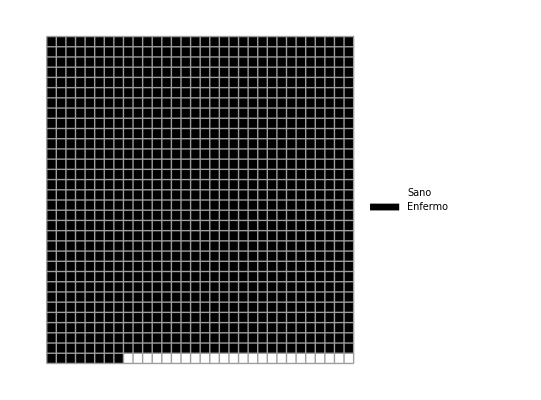

```mathematica
plt1 = PlotGroup[group,Black,PlotLegends->{"Sano","Enfermo"}]
```

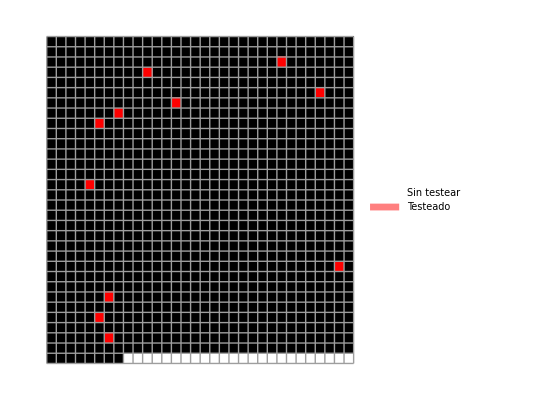

```mathematica
plt2 = PlotGroup[sampled,{Opacity[0.5],Red},PlotLegends->{"Sin testear","Testeado"}]
```

La mayoría de los resultados de las pruebas son falsos positivos.

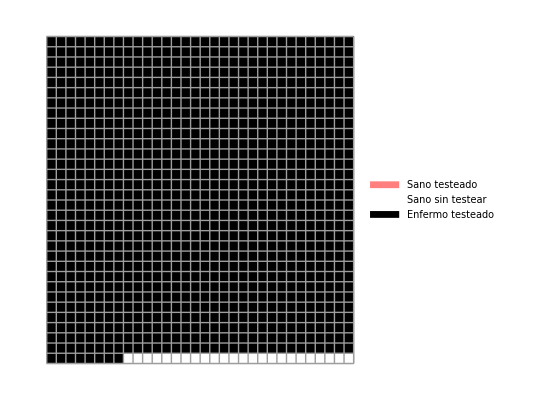

```mathematica
plt1 = PlotGroup[group,Black,PlotLegends->{"Sano sin testear","Enfermo testeado"}];
plt2 = PlotGroup[sampled,{Opacity[0.5],Red},PlotLegends->{"","Sano testeado"}];
Show[plt2,plt1]
```

La probabilidad de tener la enfermedad en caso de que la prueba de resultado positivo es

```mathematica
testedGroup = GetTestedGroup[group,sampled];
N[100*Count[testedGroup,1]/(Count[testedGroup,0]+Count[testedGroup,1])]
```

16.6667

Al hacer la prueba estadística 100000 veces se obtiene

```mathematica
tests = Table[
group = GenerateGroup[0.001,1000];
sampled = SampledGroup[group,0.01*Length[group]];
testedGroup = GetTestedGroup[group,sampled];
Count[testedGroup,1]/(Count[testedGroup,0]+Count[testedGroup,1])
,
{100000}
];
```

```mathematica
N[Mean[tests]]
```

0.0841763

La probabilidad de estar enfermo si la prueba da resultado positivo es del 10 %.

```mathematica
probSequence = Table[
group = GenerateSickGroup[0.001,100000];
testsGroups = NestList[ApplyTest,group,4];
Drop[Map[100*N[Count[#,1]/(Count[#,0]+Count[#,1])]&,testsGroups],1],
{1000}
];
```

```mathematica
means = Map[Mean,Transpose[probSequence]]
```

{9.02983,90.7845,99.9082,100.}

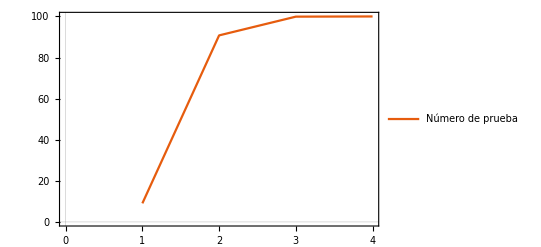

```mathematica
ListLinePlot[means,PlotTheme->"Scientific", PlotLegends->{"Número de prueba","Probabilidad de estar enfermo"}]
```